```mathematica
Clear[R,ϵ];
```

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-0.4/(-1+√((-1+R)^2+0.8 R)+R)

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

(√((-1+R)^2+0.8 R) ϵ+(-1+R) ϵ)/(2 R)

```mathematica
p=0.2
```

0.2

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,ϵ]
```

{{ϵ→(0.5 (-2.+2. R+2. √(1.-1.2 R+R^2)-(1.2 R)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2))-1. √(-(0.64 R^2 (0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2)))/((1.-1. R-1. √(1.-1.2 R+R^2))^2)+(2.-2. R-2. √(1.-1.2 R+R^2)+(1.2 R)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2)))^2)))/(0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2))},{ϵ→(0.5 (-2.+2. R+2. √(1.-1.2 R+R^2)-(1.2 R)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2))+√(-(0.64 R^2 (0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2)))/((1.-1. R-1. √(1.-1.2 R+R^2))^2)+(2.-2. R-2. √(1.-1.2 R+R^2)+(1.2 R)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2)))^2)))/(0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2))}}

```mathematica
g[R_]:=(0.5 (-2.+2. R+2. √(1.-1.2 R+R^2)-(1.2000000000000002 R)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2))-1. √(-(0.6400000000000001 R^2 (0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2)))/((1.-1. R-1. √(1.-1.2 R+R^2))^2)+(2.-2. R-2. √(1.-1.2 R+R^2)+(1.2000000000000002 R)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2)))^2)))/(0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2))
```

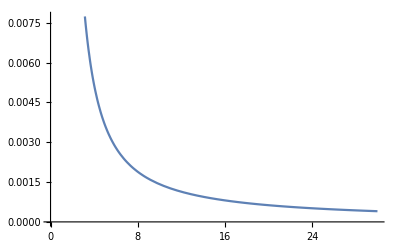

```mathematica
Plot[g[R],{R,0,30}]
```

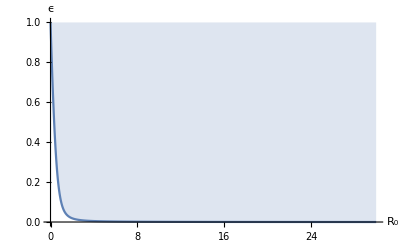

```mathematica
Plot[g[R],{R,0,30},Filling->Top,AxesLabel->{Subscript[R, 0],ϵ},PlotRange->Full]
```

```mathematica
h[R_]:=(0.5 (-2.+2. R+2. √(1.-1.2 R+R^2)-(1.2000000000000002 R)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))+(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2))+√(-(0.6400000000000001 R^2 (0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2)))/((1.-1. R-1. √(1.-1.2 R+R^2))^2)+(2.-2. R-2. √(1.-1.2 R+R^2)+(1.2000000000000002 R)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R^2)/(1.-1. R-1. √(1.-1.2 R+R^2))-(0.4 R √(1.-1.2 R+R^2))/(1.-1. R-1. √(1.-1.2 R+R^2)))^2)))/(0.5+0.2 R+0.5 R^2+0.5 √(1.-1.2 R+R^2)+0.5 R √(1.-1.2 R+R^2))
```

```mathematica
m[R_]:=g[R+1]
```

```mathematica
n[R_]:=h[R+1]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

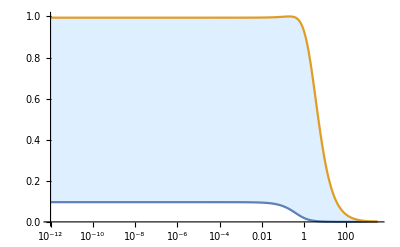

```mathematica
LogLinearPlot[{m[R],n[R]},{R,0.000000000001,3000},PlotRange->{{0,3000},{0,1}},Filling->{1->{{2},{LightBlue,White}}}]
```

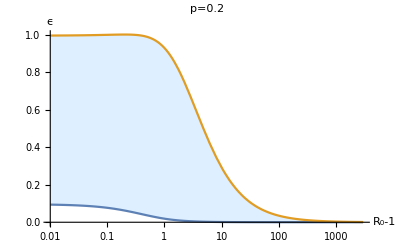

```mathematica
Show[%26,AxesLabel->{HoldForm[Subscript[R, 0]-1],HoldForm[ϵ]},PlotLabel->HoldForm[p=0.2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_2nd\\Figures\\epsilon_vs_R_0\\p=0.2.pdf",%28,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_2nd\Figures\epsilon_vs_R_0\p=0.2.pdf